```mathematica
(* MA39110 / Assignment 5 / 16MA20053 / NER ROHIT *)
ClearAll["Global`*"];
```

```mathematica
Thomas[a_,b_,c_,d_]:=Module[{c1=Range[Length[c]],d1=Range[Length[d]],x=Range[Length[b]]},
c1[[1]]=c[[1]]/b[[1]]; d1[[1]]=d[[1]]/b[[1]];
Do[
If[i≠Length[d],c1[[i]]=c[[i]]/(b[[i]]-a[[i-1]]*c1[[i-1]])];
d1[[i]]=(d[[i]]-a[[i-1]]*d1[[i-1]])/(b[[i]]-a[[i-1]]*c1[[i-1]]);
,{i,2,Length[d]}];
x[[Length[b]]]=d1[[Length[b]]];
Do[
x[[i]]=d1[[i]]-c1[[i]]*x[[i+1]];
,{i,Length[b]-1,1,-1}];
x];
Model[n0_]:=Module[{n=n0},
x0=0;xf=Pi;h=(xf-x0)/n;
y0=1/2;yf=-1/2;
A=Table[0,{x,1,n-1},{y,1,n-1}];
X=Table[x0+x*h,{x,1,n-1}];
XT=Table[x0+x*h,{x,0,n}];
B=Table[0,{x,1,n-1}];
eps=0.00001;
(*Initial Approximation: Line passing through the points (x0,y0) and (xn,yn).*)
y[x_]=(xf-x)y0/(xf-x0)+(x-x0)yf/(xf-x0)(*((Pi-1)/(Pi^2-Pi/2))x^2-((Pi^2-1/2)/(Pi^2-Pi/2))x+1/2*);
Y=N[y[XT]];
YT=Y;
While[{
Y=YT;
For[i=1,i<n,i++,
{
im=i+1;
A[[i,i]]=-(2/h^2)-2Y[[im]]+1;
B[[i]]=-(1/(4h^2))(Y[[im+1]]-Y[[im-1]])^2-Y[[im]]^2-1;
If[i≠1,A[[i,i-1]]=(1/h^2)(1+(Y[[im+1]]-Y[[im-1]])/2)];
If[i≠n-1,A[[i,i+1]]=(1/h^2)(1-(Y[[im+1]]-Y[[im-1]])/2)];
If[i==1,B[[i]]=B[[i]]-(1/h^2)y0(1+(Y[[im+1]]-Y[[im-1]])/2)];
If[i==n-1,B[[i]]=B[[i]]-(1/h^2)yf(1-(Y[[im+1]]-Y[[im-1]])/2)];
}];
YT=N[Flatten[{{y0},Thomas[Diagonal[A,-1],Diagonal[A],Diagonal[A,1],B],{yf}}]];
};N[Max[Abs[YT-Y]]]>eps];
ListPlot[Transpose[{XT,YT}]]
];
```

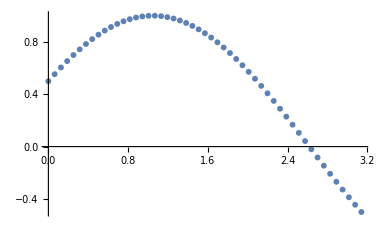

```mathematica
Model[50]
```